## Modeling Gene Expression with LacI

### Importing Data and Setting Plotting Styles

#### Data

Each entry is in the form 
{Distal Operator, -35 element, -10 element, Proximal Operator, Gene Expression without IPTG, Gene Expression with 1mM IPTG}

```mathematica
dataPcombo=Import[FileNameJoin[{NotebookDirectory[],"induce_combo.csv"}]];
```

```mathematica
dataPmultiple=Import[FileNameJoin[{NotebookDirectory[],"fig3_induce_multiple.txt"}],"TSV"];
```

#### Plotting Styles

```mathematica
(* To format String expressions *)
font[text_,size_:12,opts___]:=Style[text,FontFamily->"Times",size,opts];
```

```mathematica
(* Style options for plots *)
opts={Frame->{True,True,False,False},ImageSize->295{1,1/GoldenRatio}};
```

```mathematica
(* Styling for plot legends *)
frame[leg_]:=Framed[leg,FrameStyle->{GrayLevel[0.36]},RoundingRadius->10,FrameMargins->2];
```

#### R^2 Function

Compute R^2 of fits. Note that we compute the R^2 of Log_10[Gene Expression] in all instances because all dataPcombo are shown on a log-log plot

```mathematica
rSqaured[dataPcombo_]:=Module[{mean},
mean=Mean[dataPcombo[[All,2]]];
Round[1-Total[(#[[1]]-#[[2]])^2&/@dataPcombo]/Total[(#[[2]]-mean)^2&/@dataPcombo],0.01]
]
```

### Fitting Entire Data Set: Gene Expression at 0mM and 1mM IPTG

Assuming the following states for the promoter and their corresponding Boltzmann weights and levels of gene expression (GE)

-Graphics-

Assumptions of the model:

The free energy of LacI binding to a distal (E_dist) or proximal (E_prox) site depends purely on the binding site sequence and not its location. This free energy accounts for both the entropy lost and the energy gained by binding

The free energy of looping (E_loop) accounts both for the (unfavorable) energetic cost of looping and the (favorable) entropic cost, since the loss in the repressor’s entropy is much less for the bivalent binding that occurs during looping than for monovalent binding when the repressor first associates onto the DNA

Gene expression was measured both in the presence and absence of IPTG (a gratuitous inducer that inactivates LacI). All LacI is assumed to be completely active in the absence of IPTG, and each repressor has a probability p of being active in the presence of 1mM IPTG. Therefore, the form of gene expression at 1mM IPTG will be identical to that at 0mM IPTG, but the free energies of LacI binding will all be modified to E_prox→E_prox-Log[p], E_dist→E_dist-Log[p], and E_loop→E_loop-Log[p] (where this last factor accounts for the fact that only a single LacI is involved in looping)

RNAP binds at the -35 and -10 sites, and it is assumed to either be unbound or to simultaneously bind at both sites (ignoring the states where only the -35 or only the -10 sites are bound, since adding these effects would negligibly change the model results)

Gene expression is assumed to take on a small value r_min characterizing a combination of background noise. If RNAP is bound to the operator of interest and LacI is not bound to the proximal site, gene expression increases to the value r_max

With these assumptions, gene expression is given by

Gene Expression=(r_min(Z_notProx+Z_prox+ⅇ^(-β (E_-35+E_-10))Z_prox)+r_max ⅇ^(-β (E_-35+E_-10))Z_notProx)/((1+ⅇ^(-β (E_-35+E_-10)))(Z_Prox+Z_notProx))

where

Z_prox=ⅇ^(-β E_prox)+ⅇ^(-β (E_prox+E_dist))+ⅇ^(-β (E_prox+E_dist+E_loop))

is the sum of Boltzmann weights of the states where LacI is bound to the proximal site (and hence inhibits gene expression) and

Z_notProx=1+ⅇ^(-β E_dist)

where LacI is not bound to the proximal site so that, if RNAP is bound, gene expression increases from r_min to r_max

```mathematica
(* Consider all the dataPcombo *)
source=Cases[dataPcombo,{_,_,_,_,__}];
(* Unique promoter elements *)
op35=Reverse@Union@source[[All,2]];
op10=Reverse@Union@source[[All,3]];
proximal=(Union@source[[All,4]])[[{1,2,3,5,6,7,8,9,10,4}]];
distal=proximal;
(* The first element is the concentration (in mM) of IPTG. The next Length@op35 elements dicate which -35 site is used; the next Length@op10 elements dictate which -10 is used; the next Length@proximal determine which proximal site is used; the last element is gene expression either at 0mM or 1mM IPTG *)
elements[list_,val_]:=UnitVector[Length@list,Position[list,val][[1,1]]]
(* Considering both dataPcombo at 0mM IPTG and 1mM IPTG *)
fitData=Join[Flatten[{0,elements[distal,#[[1]]],elements[op35,#[[2]]],elements[op10,#[[3]]],elements[proximal,#[[4]]],Log[10,#[[-2]]]}]&/@source,Flatten[{1,elements[distal,#[[1]]],elements[op35,#[[2]]],elements[op10,#[[3]]],elements[proximal,#[[4]]],Log[10,#[[-1]]]}]&/@source];
```

```mathematica
(* Set up the fit function *)
selectDistal=Total[a[#]ϵ[proximal[[#]]]&/@Range@Length@distal];
select35=Total[b[#]ϵ[op35[[#]]]&/@Range@Length@op35];
select10=Total[c[#]ϵ[op10[[#]]]&/@Range@Length@op10];
selectProximal=Total[d[#]ϵ[proximal[[#]]]&/@Range@Length@proximal];
Zprox=E^(-(selectProximal-IPTG pLog))+E^(-(selectProximal+selectDistal-2IPTG pLog))+E^(-(selectProximal+selectDistal+loop-IPTG pLog));
ZnotProx=1+E^(-(selectDistal-IPTG pLog));
Znumerator=(E^rMinLog ZnotProx+E^rMinLog Zprox+E^rMinLog E^(-(select35+select10))Zprox)+E^rMaxLog E^(-(select35+select10))ZnotProx;
Zdenominator=(1+E^(-(select35+select10)))(Zprox+ZnotProx);
parameterDegeneracy={
(* The free energies of the four -10's can always be increased by any amount provided the free energies of the four -35's is decreased by this same amount. To eliminate this parameter degeneracy, we arbitrarily fix the -Subscript[10, cons] sequence to have free energy zero, so that the free energies of all the -10's and the -35's is relative to this value *)
ϵ["minus10cons"]->0.,
(* The scrambled sequence is assumed to not be able to bind to LacI *)
ϵ["lacOscram"]->10.};
fitFunction=Log[10,Znumerator/Zdenominator]/.parameterDegeneracy;
```

```mathematica
(* Initial values for nonlinear fitting *)
initialGuess={ϵ["minus10cons"]->0.,ϵ["lacOscram"]->10.,rMinLog->-0.0256,rMaxLog->3.442,loop->-3.048,pLog->-5.366,ϵ["lacO1"]->-0.392,ϵ["lacO2"]->2.934,ϵ["lacO3"]->1.951,ϵ["lacOsym"]->-2.352,ϵ["O1_rightSym"]->2.803,ϵ["O2_leftSym"]->4.726,ϵ["O2_rightSym"]->1.410,ϵ["O3_leftSym"]->3.214,ϵ["O3_rightSym"]->3.883,ϵ["minus35cons"]->-1.819,ϵ["minus35_33T"]->1.766,ϵ["minus35_31A_32C"]->0.749,ϵ["minus35_30C_33T"]->3.587,ϵ["minus10_7A"]->3.928,ϵ["minus10_12G"]->3.693,ϵ["minus10_12A"]->4.929};
initialValues=Join[
(* Initial guesses for Subscript[r, min]=E^rMinLog, Subscript[r, max]=E^rMaxLog, Subscript[E, loop], and p=E^pLog *)
{{rMinLog,-0.9},{rMaxLog,4.},{loop,-6},{pLog,-5.3}},
(* Initial guesses for the -35 and -10 elements *)
{ϵ[#],ϵ[#]/.initialGuess}&/@distal,
{ϵ[#],ϵ[#]/.initialGuess}&/@op35,
{ϵ[#],ϵ[#]/.initialGuess}&/@op10
];
dependentParameters=Join[{IPTG},a[#]&/@Range@Length@distal,b[#]&/@Range@Length@op35,c[#]&/@Range@Length@op10,d[#]&/@Range@Length@proximal];
fitRefinedEnergyMatrix=Quiet@NonlinearModelFit[fitData,{fitFunction(*,rMaxLog==6*)},initialValues,dependentParameters];
(* Summary of the best fit parameters *)bestFitParameters=Join[parameterDegeneracy,DeleteCases[fitRefinedEnergyMatrix["BestFitParameters"],f_/;MemberQ[parameterDegeneracy[[All,1]],First@f]]];
{fitRefinedEnergyMatrix["RSquared"],bestFitParameters}
```

{0.836668,{ϵ[minus10cons]→0.,ϵ[lacOscram]→10.,rMinLog→-0.128652,rMaxLog→3.22459,loop→-2.48503,pLog→-3.5672,ϵ[lacO1]→-0.225705,ϵ[lacO2]→3.90557,ϵ[lacO3]→2.00776,ϵ[lacOsym]→-2.08686,ϵ[O1_rightSym]→3.0125,ϵ[O2_leftSym]→27.8844,ϵ[O2_rightSym]→1.58303,ϵ[O3_leftSym]→3.76481,ϵ[O3_rightSym]→25.9588,ϵ[minus35cons]→-1.95698,ϵ[minus35_33T]→1.69817,ϵ[minus35_31A_32C]→0.664269,ϵ[minus35_30C_33T]→3.57895,ϵ[minus10_7A]→3.99919,ϵ[minus10_12G]→3.7739,ϵ[minus10_12A]→5.02711}}

Figure3A.csv

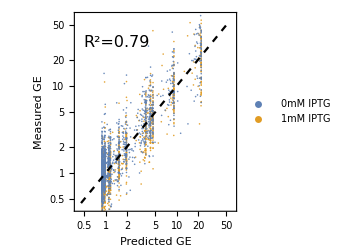

```mathematica
(* Plot the results for all promoters *)
predictionsRefinedEnergyMatrix={#[[Length@source+1;;]],#[[;;Length@source]]}&[Transpose@{fitRefinedEnergyMatrix["PredictedResponse"],fitRefinedEnergyMatrix["Response"]}];
Export["Figure3A.csv",predictionsRefinedEnergyMatrix]
leg=PointLegend[ColorData[97]/@Range@2,font/@{"0mM IPTG","1mM IPTG"},LegendFunction->frame,Spacings->{0.2,0.2}];
plot=Show[ListLogLogPlot[10^predictionsRefinedEnergyMatrix,FrameLabel->(font[#,14]&/@{"Predicted GE","Measured GE"})(*,PlotLabel->font["Bivalent RNAP Binding",14]*),PlotRange->{{10^-0.4,10^1.8},{10^-0.4,10^1.8}},AspectRatio->1,ImageSize->250,Epilog->{Text[font["R^2="<>ToString@rSqaured[Transpose@{fitRefinedEnergyMatrix["PredictedResponse"],fitRefinedEnergyMatrix["Response"]}],16],{Log[10^0.15],Log[10^1.5]}]},PlotLegends->Placed[leg,Scaled[{{0.77,0.18},{0.5,0.5}}]],PlotStyle->({ColorData[97][#],Opacity[0.9]}&/@{2,1}),Evaluate@opts],LogLogPlot[x,{x,10^-0.35,10^1.75},PlotStyle->{Black,Dashed}]]
```

#### Parameter Values

```mathematica
round=ReplacePart[ConstantArray[0.01,Length@bestFitParameters],{2->0.0001,4->0.001}];
parameterValues=List@@If[StringTake[ToString[#[[1]]],{-3,-1}]=="Log",StringTake[ToString[#[[1]]],{1,-4}]->E^(#[[2]]),ToString[#[[1]]]->#[[2]]]&/@Sort[bestFitParameters/.s_String/;StringMatchQ[s,"O"~~__]:>"lac"<>s];
parameterValues[[All,2]]=MapIndexed[Round[#,round[[First@#2]]]&,parameterValues[[All,2]]]/.{10.->∞};
parameterValues[[All,1]]=StringReplace[parameterValues[[All,1]],{"rMax"->"r_max","rMin"->"r_min","ϵ[minus10_"~~f__~~"]":>Row[{Subscript["E[-10",f],"]"}],"ϵ[minus35_"~~f__~~"]":>Row[{Subscript["E[-35",f],"]"}],"ϵ[lacO"~~num_~~"_"~~f__~~"]":>Row[{Subsuperscript["E[lac","O"<>num,f],"]"}],"ϵ[minus"~~num__~~"cons]":>Row[{Subscript["E[-"<>num,"cons"],"]"}],"ϵ[lacO"~~num_~~"]":>Row[{Subscript["E[lac","O"<>num],"]"}],"ϵ[lacOscram]":>Row[{Subscript["E[lac","Oscram"],"]"}],"ϵ[lacOsym]":>Row[{Subscript["E[lac","Osym"],"]"}]}]/.{StringExpression->Identity,"p"->"p_act^repressor","loop"->"E_loop"};
(* Rearrange parameters *)
parameterValues=Join[parameterValues[[{4,3,1,2}]],parameterValues[[5;;14]],parameterValues[[{18,17,15,16,22,19,20,21}]]];
parameterResults=Text@Grid[Prepend[parameterValues,Style[#,Bold]&/@{"Parameter","Value"}],Background->{None,{Lighter[Yellow,.9],Join[ConstantArray[RGBColor[0.8, 0.9, 0.9],{2}],ConstantArray[GrayLevel[1],{2}],ConstantArray[RGBColor[0.8, 0.9, 0.9],{10}],ConstantArray[GrayLevel[1],{4}],ConstantArray[RGBColor[0.8, 0.9, 0.9],{4}]]}},Dividers->{{Darker[Gray,.6],{Lighter[Gray,.5]},Darker[Gray,.6]},{Darker[Gray,.6],Darker[Gray,.6],{False},Darker[Gray,.6]}},Alignment->Center,Frame->Darker[Gray,.6],ItemStyle->14,Spacings->{Automatic,.8}]
```

Parameter | Value
r_min | 0.879
r_max | 25.14
E_loop | -2.49
p_act^repressor | 0.0282
(E[lac)_O1] | -0.23
(E[lac)_O1^rightSym] | 3.01
(E[lac)_O2] | 3.91
(E[lac)_O2^leftSym] | 27.88
(E[lac)_O2^rightSym] | 1.58
(E[lac)_O3] | 2.01
(E[lac)_O3^leftSym] | 3.76
(E[lac)_O3^rightSym] | 25.96
(E[lac)_Oscram] | ∞
(E[lac)_Osym] | -2.09
(E[-10)_cons] | 0.
(E[-10)_(7A)] | 4.
(E[-10)_(12A)] | 5.03
(E[-10)_(12G)] | 3.77
(E[-35)_cons] | -1.96
(E[-35)_(30C_33T)] | 3.58
(E[-35)_(31A_32C)] | 0.66
(E[-35)_(33T)] | 1.7

### Fitting Entire Data Set: Predicting Leakiness and Saturation

#### Gene Expression as a Function of LacI Binding

```mathematica
formatM35[m35_]:=Subscript["-35",StringReplace[StringTake[m35,{If[StringTake[m35,{8,8}]==="_",9,8],-1}],"_"->","]]
formatM10[m10_]:=Subscript["-10",StringReplace[StringTake[m10,{If[StringTake[m10,{8,8}]==="_",9,8],-1}],"_"->","]]
fullResults[m35_,m10_,showPlotLabel_,showPlotLegend_]:=(
Zprox=E^(-(ϵprox-IPTG pLog))+E^(-(ϵprox+ϵdist-2IPTG pLog))+E^(-(ϵprox+ϵdist+loop-IPTG pLog));
ZnotProx=1+E^(-(ϵdist-IPTG pLog));
Znumerator=(E^rMinLog ZnotProx+E^rMinLog Zprox+E^rMinLog E^(-(ϵ[m35]+ϵ[m10]))Zprox)+E^rMaxLog E^(-(ϵ[m35]+ϵ[m10]))ZnotProx;
Zdenominator=(1+E^(-(ϵ[m35]+ϵ[m10])))(Zprox+ZnotProx);
fitFunction0mMIPTG=Znumerator/Zdenominator/.bestFitParameters/.IPTG->0;
fitFunction1mMIPTG=Znumerator/Zdenominator/.bestFitParameters/.IPTG->1;
(* Plot the inferred LacI binding energies from the experimental dataPcombo versus its gene expression *)
plotData={{ϵ@#[[1]],ϵ@#[[4]],#[[-2]]}&/@Cases[source,{_,m35,m10,__}],{ϵ@#[[1]],ϵ@#[[4]],#[[-1]]}&/@Cases[source,{_,m35,m10,__}]}/.bestFitParameters;
With[{opts=Join[If[showPlotLabel,{PlotLabel->Row[Style[#,18]&/@{formatM35[m35],"/",formatM10[m10]}]},{}],If[showPlotLegend,{PlotLegends->Placed[{"0mM IPTG","1mM IPTG"},Below]},{}]]},
Show[Plot3D[{fitFunction0mMIPTG,fitFunction1mMIPTG},{ϵdist,-5,10},{ϵprox,-5,10},ScalingFunctions->"Log",PlotStyle->({ColorData[97][#],Opacity[0.5]}&/@Range@2),AxesEdge->{{-1,-1},{1,-1},{-1,-1}},ViewPoint->{1.3,-2.9,1.2},AxesLabel->(font[#,If[showPlotLabel,18,20]]&/@{"ϵ_dist","ϵ_prox","GE"}),ImageSize->Medium,TicksStyle->Directive["Label",If[showPlotLabel,14,18]],PlotRange->{{-5,10.5},{-5,10.5},{0.5,75.}},opts],ListPointPlot3D[plotData,ScalingFunctions->"Log"](*,PlotRange->All*)]
]
)
```

Results for the -35_cons/-10_cons RNAP promoter. Un-comment the following line to see the results for the -35_(30,C,33,T)/-10_(12,A) promoter (and all other promoters can be seen by similarly modifying the code)

```mathematica
fullResults["minus35cons","minus10cons",True,True]
Export["Figure3B.csv",plotData]
(*fullResults["minus35_30C_33T","minus10_12A",True,True]*)
```

-Graphics3D-

Figure3B.csv

Un-comment and run the following code if you want to see the resulting plots for all combinations of RNAP binding sites

```mathematica
(*Grid@Partition[fullResults[#[[1]],#[[2]],True,False]&/@Union@source[[All,{2,3}]],4]*)
```

#### Fold-Change as a Function of LacI Binding

```mathematica
formatM35[m35_]:=Subscript["-35",StringReplace[StringTake[m35,{If[StringTake[m35,{8,8}]==="_",9,8],-1}],"_"->","]]
formatM10[m10_]:=Subscript["-10",StringReplace[StringTake[m10,{If[StringTake[m10,{8,8}]==="_",9,8],-1}],"_"->","]]
fullResultsFoldChange[m35_,m10_,showPlotLabel_,showPlotLegend_]:=(
Zprox=E^(-(ϵprox-IPTG pLog))+E^(-(ϵprox+ϵdist-2IPTG pLog))+E^(-(ϵprox+ϵdist+loop-IPTG pLog));
ZnotProx=1+E^(-(ϵdist-IPTG pLog));
Znumerator=(E^rMinLog ZnotProx+E^rMinLog Zprox+E^rMinLog E^(-(ϵ[m35]+ϵ[m10]))Zprox)+E^rMaxLog E^(-(ϵ[m35]+ϵ[m10]))ZnotProx;
Zdenominator=(1+E^(-(ϵ[m35]+ϵ[m10])))(Zprox+ZnotProx);
fitFunction0mMIPTG=Znumerator/Zdenominator/.bestFitParameters/.IPTG->0;
fitFunction1mMIPTG=Znumerator/Zdenominator/.bestFitParameters/.IPTG->1;
(* Plot the inferred LacI binding energies from the experimental dataPcombo versus its gene expression *)
plotData={ϵ@#[[1]],ϵ@#[[4]],(#[[-1]])/(#[[-2]])}&/@Cases[source,{_,m35,m10,__}]/.bestFitParameters;
With[{opts=Join[If[showPlotLabel,{PlotLabel->Row[Style[#,18]&/@{formatM35[m35],"/",formatM10[m10]}]},{}],If[showPlotLegend,{PlotLegends->Placed[{"Fold Change"},Below]},{}]]},
Show[Plot3D[fitFunction1mMIPTG/fitFunction0mMIPTG,{ϵdist,-5,10},{ϵprox,-5,10},ScalingFunctions->"Log",PlotStyle->({ColorData[97][3],Opacity[0.5]}),AxesEdge->{{-1,-1},{1,-1},{-1,-1}},ViewPoint->{1.3,-2.9,1.2},AxesLabel->(font[#,If[showPlotLabel,18,20]]&/@{"ϵ_dist","ϵ_prox","FC"}),ImageSize->Medium,TicksStyle->Directive["Label",If[showPlotLabel,14,18]],PlotRange->{{-5,10.5},{-5,10.5},{0.5,20.}},opts],ListPointPlot3D[plotData,ScalingFunctions->"Log",PlotStyle->ColorData[97][3]]]
]
)
```

Results for the -35_cons/-10_cons RNAP promoter. Un-comment the following line to see the results for the -35_(30,C,33,T)/-10_(12,A) promoter (and all other promoters can be seen by similarly modifying the code)

```mathematica
fullResultsFoldChange["minus35cons","minus10cons",True,True]
Export["Figure3C.csv",plotData]
(*fullResultsFoldChange["minus35_30C_33T","minus10_12A",True,True]*)
```

-Graphics3D-

Figure3C.csv

Un-comment and run the following code if you want to see the resulting plots for all combinations of RNAP binding sites

```mathematica
(*Grid@Partition[fullResultsFoldChange[#[[1]],#[[2]],True,False]&/@Union@source[[All,{2,3}]],4]*)
```

### Training on a Subset of Data: Gene Expression at 0mM and 1mM IPTG

We now utilize a fraction of the promoter architectures to determine the parameter values in our model and using the remaining promoters to test our model predictions.

```mathematica
(* Consider all the data *)
source=Cases[dataPcombo,{_,_,_,_,__}];
(* Unique promoter elements *)
op35=Reverse@Union@source[[All,2]];
op10=Reverse@Union@source[[All,3]];
proximal=(Union@source[[All,4]])[[{1,2,3,5,6,7,8,9,10,4}]];
distal=proximal;
(* The first element is the concentration (in mM) of IPTG. The next Length@op35 elements dicate which -35 site is used; the next Length@op10 elements dictate which -10 is used; the next Length@proximal determine which proximal site is used; the last element is gene expression either at 0mM or 1mM IPTG *)
elements[list_,val_]:=UnitVector[Length@list,Position[list,val][[1,1]]]
(* Considering both data at 0mM IPTG and 1mM IPTG *)
fitData=Join[Flatten[{0,elements[distal,#[[1]]],elements[op35,#[[2]]],elements[op10,#[[3]]],elements[proximal,#[[4]]],Log[10,#[[-2]]]}]&/@source,Flatten[{1,elements[distal,#[[1]]],elements[op35,#[[2]]],elements[op10,#[[3]]],elements[proximal,#[[4]]],Log[10,#[[-1]]]}]&/@source];
```

```mathematica
(* Set up the fit function *)
selectDistal=Total[a[#]ϵ[proximal[[#]]]&/@Range@Length@distal];
select35=Total[b[#]ϵ[op35[[#]]]&/@Range@Length@op35];
select10=Total[c[#]ϵ[op10[[#]]]&/@Range@Length@op10];
selectProximal=Total[d[#]ϵ[proximal[[#]]]&/@Range@Length@proximal];
Zprox=E^(-(selectProximal-IPTG pLog))+E^(-(selectProximal+selectDistal-2IPTG pLog))+E^(-(selectProximal+selectDistal+loop-IPTG pLog));
ZnotProx=1+E^(-(selectDistal-IPTG pLog));
Znumerator=(E^rMinLog ZnotProx+E^rMinLog Zprox+E^rMinLog E^(-(select35+select10))Zprox)+E^rMaxLog E^(-(select35+select10))ZnotProx;
Zdenominator=(1+E^(-(select35+select10)))(Zprox+ZnotProx);
parameterDegeneracy={
(* The free energies of the four -10's can always be increased by any amount provided the free energies of the four -35's is decreased by this same amount. To eliminate this parameter degeneracy, we arbitrarily fix the -Subscript[10, cons] sequence to have free energy zero, so that the free energies of all the -10's and the -35's is relative to this value *)
ϵ["minus10cons"]->0.,
(* The scrambled sequence is assumed to not be able to bind to LacI *)
ϵ["lacOscram"]->10.};
fitFunction=Log[10,Znumerator/Zdenominator]/.parameterDegeneracy;
```

```mathematica
(* Initial values for nonlinear fitting *)
initialGuess={ϵ["minus10cons"]->0.,ϵ["lacOscram"]->10.,rMinLog->-0.0256,rMaxLog->3.442,loop->-3.048,pLog->-5.366,ϵ["lacO1"]->-0.392,ϵ["lacO2"]->2.934,ϵ["lacO3"]->1.951,ϵ["lacOsym"]->-2.352,ϵ["O1_rightSym"]->2.803,ϵ["O2_leftSym"]->4.726,ϵ["O2_rightSym"]->1.410,ϵ["O3_leftSym"]->3.214,ϵ["O3_rightSym"]->3.883,ϵ["minus35cons"]->-1.819,ϵ["minus35_33T"]->1.766,ϵ["minus35_31A_32C"]->0.749,ϵ["minus35_30C_33T"]->3.587,ϵ["minus10_7A"]->3.928,ϵ["minus10_12G"]->3.693,ϵ["minus10_12A"]->4.929};
initialValues=Join[
(* Initial guesses for Subscript[r, min]=E^rMinLog, Subscript[r, max]=E^rMaxLog, Subscript[E, loop], and p=E^pLog *)
{{rMinLog,-0.9},{rMaxLog,4.},{loop,-6},{pLog,-5.3}},
(* Initial guesses for the -35 and -10 elements *)
{ϵ[#],ϵ[#]/.initialGuess}&/@distal,
{ϵ[#],ϵ[#]/.initialGuess}&/@op35,
{ϵ[#],ϵ[#]/.initialGuess}&/@op10
];
dependentParameters=Join[{IPTG},a[#]&/@Range@Length@distal,b[#]&/@Range@Length@op35,c[#]&/@Range@Length@op10,d[#]&/@Range@Length@proximal];
```

Train the model using a subset of the data and test it on the remaining data

```mathematica
trainModel[dataFraction_]:=Quiet@(
SeedRandom[12345];
Table[
dataTraining=RandomSample[fitData,Round[dataFraction Length@fitData]];
fitRefinedEnergyMatrix=Quiet@NonlinearModelFit[dataTraining,{fitFunction},initialValues,dependentParameters];
rSqaured[{fitFunction/.Thread[dependentParameters->Most@#],Last@#}&/@Complement[fitData,dataTraining]/.fitRefinedEnergyMatrix["BestFitParameters"]]
,{20}]
)
```

The following commented code runs the training on 20 different subsets of data for each fraction. This code takes several minutes to run, so for convenience I have canned the results below.

```mathematica
(*res=Table[{frac,trainModel[frac]},{frac,{0.01,0.03,0.05,0.1,0.3,0.5,0.7,0.9}}]*)
```

FigureS5A.csv

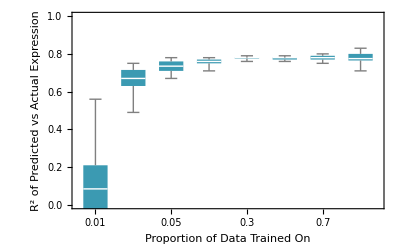

```mathematica
res={{0.01,{0.07,-0.35,0.07,0.11,Indeterminate,-1.86,0.38,0.18,0.39,0.56,0.33,-0.3,-0.84,Indeterminate,0.21,0.1,-0.27,0.12,-0.29,0.05}},{0.03,{0.74,0.67,0.72,0.66,0.62,0.68,0.49,0.55,0.62,0.70,0.75,0.63,0.72,0.67,0.71,0.66,0.7,0.64,0.72,0.63}},{0.05,{0.75,0.71,0.67,0.71,0.71,0.71,0.78,0.75,0.76,0.68,0.74,0.72,0.69,0.76,0.69,0.76,0.73,0.76,0.74,0.77}},{0.1,{0.77,0.75,0.71,0.76,0.76,0.75,0.76,0.78,0.77,0.78,0.74,0.77,0.75,0.74,0.77,0.77,0.76,0.76,0.77,0.77}},{0.3,{0.77,0.78,0.78,0.78,0.78,0.78,0.78,0.78,0.78,0.79,0.76,0.78,0.78,0.77,0.78,0.78,0.77,0.78,0.77,0.78}},{0.5,{0.77,0.78,0.77,0.78,0.76,0.78,0.77,0.79,0.79,0.78,0.77,0.79,0.78,0.77,0.77,0.77,0.78,0.76,0.78,0.79}},{0.7,{0.78,0.77,0.8,0.78,0.79,0.79,0.77,0.78,0.8,0.79,0.78,0.76,0.8,0.75,0.77,0.76,0.8,0.78,0.78,0.77}},{0.9,{0.77,0.78,0.79,0.77,0.8,0.83,0.77,0.76,0.81,0.71,0.8,0.81,0.77,0.79,0.77,0.8,0.82,0.75,0.75,0.76}}};
Export["FigureS5A.csv",res]
plot=BoxWhiskerChart[res[[All,2]],ChartLabels->res[[All,1]],ChartStyle->RGBColor[0.23165676958670167, 0.6043872300788907, 0.6980479914002558],FrameLabel->(Style[#,12]&/@{"Proportion of Data Trained On","R^2 of Predicted vs Actual Expression"}),FrameStyle->12,PlotRange->{0,1},PlotRangeClipping->True]
```

### Predicting Expression for the Double Distal Promoter Architecture

#### Assuming the Distal and Distal+ sites cannot be simultaneously bound by LacI

Gene Expression=(r_min(Z_notProx+Z_prox+ⅇ^(-β (E_-35+E_-10))Z_prox)+r_max ⅇ^(-β (E_-35+E_-10))Z_notProx)/((1+ⅇ^(-β (E_-35+E_-10)))(Z_Prox+Z_notProx))

where

Z_prox=ⅇ^(-β E_prox)+ⅇ^(-β (E_prox+E_dist))+ⅇ^(-β (E_prox+E_(dist^+)))
                     +ⅇ^(-β (E_prox+E_dist+E_loop))+ⅇ^(-β (E_prox+E_(dist^+)+E_loop))

Z_notProx=1+ⅇ^(-β E_dist)+ⅇ^(-β E_(dist^+))

```mathematica
predictions=(
Zprox=E^(-(ϵ[#[[7]]]-IPTG pLog))+E^(-(ϵ[#[[7]]]+ϵ[#[[3]]]-2IPTG pLog))+E^(-(ϵ[#[[7]]]+ϵ[#[[4]]]-2IPTG pLog))+E^(-(ϵ[#[[7]]]+ϵ[#[[3]]]+loop-IPTG pLog))+E^(-(ϵ[#[[7]]]+ϵ[#[[4]]]+loop-IPTG pLog));
ZnotProx=1+E^(-(ϵ[#[[3]]]-IPTG pLog))+E^(-(ϵ[#[[4]]]-IPTG pLog));
Znumerator=(E^rMinLog ZnotProx+E^rMinLog Zprox+E^rMinLog E^(-(ϵ[#[[5]]]+ϵ[#[[6]]]))Zprox)+E^rMaxLog E^(-(ϵ[#[[5]]]+ϵ[#[[6]]]))ZnotProx;
Zdenominator=(1+E^(-(ϵ[#[[5]]]+ϵ[#[[6]]])))(Zprox+ZnotProx);
{{Znumerator/Zdenominator/.IPTG->0,#[[8]]},{Znumerator/Zdenominator/.IPTG->1,#[[9]]}}
)&/@Rest@dataPmultiple/.bestFitParameters;
Export["FigureS5B.csv",predictions]
```

FigureS5B.csv

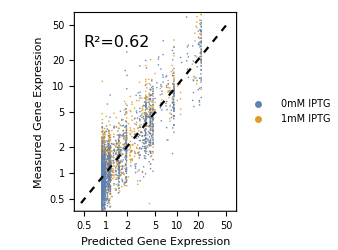

```mathematica
(* Plot the results for all promoters *)
leg=PointLegend[ColorData[97]/@Range@2,font[#,16]&/@{"0mM IPTG","1mM IPTG"},LegendFunction->frame,Spacings->{0.2,0.4},Alignment->{Center,Center}];
plot=Show[ListLogLogPlot[Transpose@predictions,FrameLabel->(font[#,16]&/@{"Predicted Gene Expression","Measured Gene Expression"}),PlotRange->{{10^-0.4,10^1.8},{10^-0.4,10^1.8}},AspectRatio->1,ImageSize->250,Epilog->{Text[font["R^2="<>ToString@Round[rSqaured[Join@@predictions],0.01],16],{Log[10^0.15],Log[10^1.5]}]},PlotLegends->Placed[leg,Scaled[{{0.75,0.175},{0.5,0.5}}]],FrameTicksStyle->14,PlotStyle->({ColorData[97][#],Opacity[0.9]}&/@{2,1}),Evaluate@opts],LogLogPlot[x,{x,10^-0.35,10^1.75},PlotStyle->{Black,Dashed}]]
```